```mathematica
NN =3
```

3

```mathematica
m0[a_] := ⅇ^(1/NN Log[a])
σ0[a_] := ⅇ^(1/NN Log[ 1 + a])

mj[a_] := m0[a] ⅇ^(2 π ⅈ j / NN)
σ1[a_] := σ0[a]  ⅇ^((2 π ⅈ)/NN)
CMS[a_] := (NN σ0[a] ( ⅇ^((2 π ⅈ)/NN) - 1) + ∑_(j=0)^(NN-1) mj[a] ( Log[ σ1[a] - mj[a] ] - Log [ σ0[a] - mj[a] ] ))/(m0[a] ( ⅇ^((2 π ⅈ)/NN) - 1))
```

{a→9.89588-2.17318×10^-14 ⅈ}

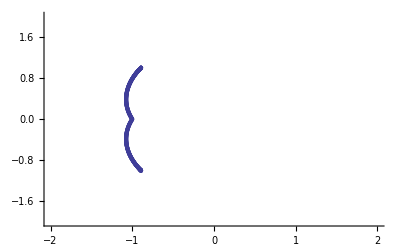

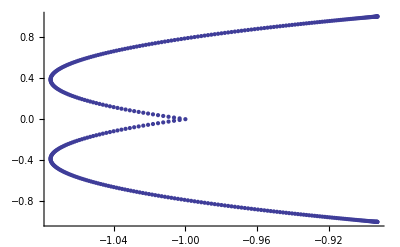

```mathematica
MM= 400;
XY  = Table[{Null, Null}, {MM}];
centre = 180;
width = 180;
For [ j = 0, j < MM, j++, 
ϕ = π/180(centre - width/2+ (width j)/MM);
a0 = -1 + 1.0 ⅇ^(ⅈ ϕ);
 z = a /. FindRoot[ { Re[CMS[a]] == 0 }, {a, a0}];
XY[[j+1]] = { Re[z], Im[z] };
 ];
FindRoot[{CMS[a] == 0}, {a, 1.0}]
ListPlot[XY,PlotRange->{{-2.0,2},{-2.0,2.0}}]
ListPlot[XY]
```